# Code for “A Vine Copula Based Multiple Dependent Convolution for High-Dimensional Power System Probabilistic Analysis”

A note of my  “Project C”, which contains many works that relates to the  convolution and copula.
Han Wu, Hohai University, China
E-mail: wuhan@hhu.edu.cn 
Working on this project During <8th Mar 2021, 9th Mar 2021 >
Copyrights reserved

### 0. 初始化

```mathematica
directory = "D:\\OneDrive - 河海大学\\Data"; (*Mathematica 工作区域*)
(*Import these R libraries*)
Needs["RLink`"];
InstallR[
  "RHomeLocation" -> "C:\\Program Files\\R\\R-4.0.4",
  "RVersion" -> "4.0.4", 
  "NativeLibLocation" -> "C:\\Program Files\\R\\R-4.0.4\\library\\rJava\\jri\\x64"]
ExternalEvaluate["R", "library(copula)"];
ExternalEvaluate["R", "library(VineCopula)"];
ExternalEvaluate["R", "library(rvinecopulib)"];
ExternalEvaluate["R", "library(mvQuad)"];
```

```mathematica
Needs["MATLink`"] (*打开Matlab*)
SetOptions[MATLink, "Force32BitEngine" -> False]
OpenMATLAB[]
```

### 1. 导入数据

```mathematica
MEvaluate["cd 'D:\\OneDrive - Personal\\OneDrive\\Data\\2018年苏州光伏数据\\'"]
MEvaluate["load '18个光伏出力.mat'"];MEvaluate["load '18光伏出力去0.mat'"];MEvaluate["load '18个光伏容量.mat'"]
pvdatafull = MGet["pvdata"];pvdata = MGet["pvdata0"];pvcap = MGet["pvcap"];
(*重新排列光伏数据，使得光伏最大出力从小到大排列*)
pvdata = pvdata[[All,1;;10]];
pvdata = SortBy[pvdataᵀ,Max]ᵀ;
TransPVdata=Transpose[pvdata];
RSet["pvdata",pvdata]; (*send all data to R*)
Print["Number of data points = ",Length[pvdata]];
```

Number of data points = 19149

```mathematica
(*10个光伏出力的KDE*)
edistKDE = Table[SmoothKernelDistribution[pvdata[[All,i]]],{i,1,10}];
```

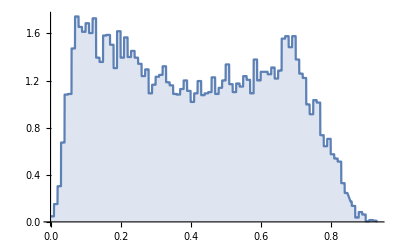
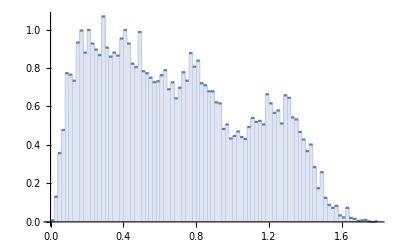
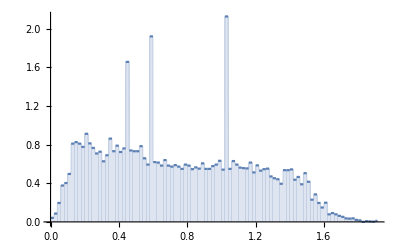
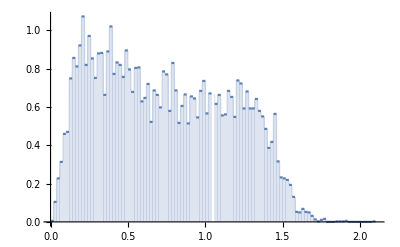
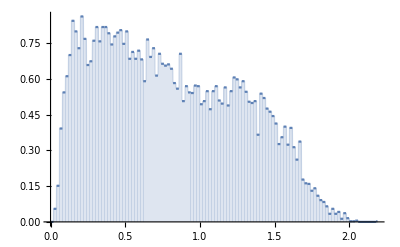
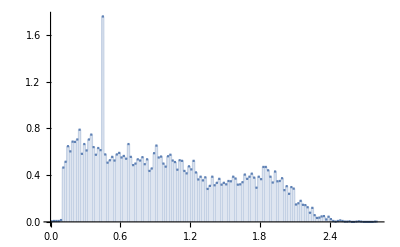
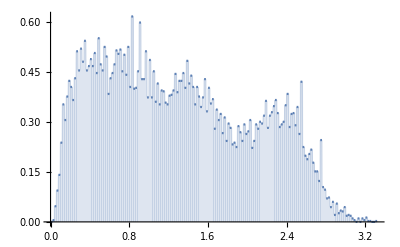
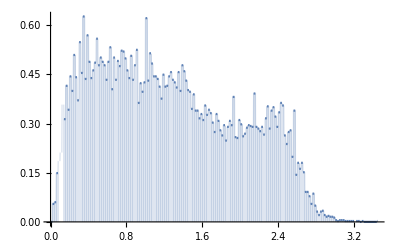

```mathematica
(*10个光伏出力的HistgreamDistbution*)
edistHis = Table[HistogramDistribution[pvdata[[All,i]],100],{i,1,10}];
Table[Plot[PDF[edistHis[[i]],x],{x,0,Max@pvdata[[All,i]]},Filling->Axis],{i,1,10}]
```

```mathematica
REvaluate["{
colnames(pvdata) <- c(\"PV1\", \"PV2\", \"PV3\", \"PV4\", \"PV5\", \"PV6\", \"PV7\", \"PV8\",\"PV9\",\"PV10\");
pesudata <- pseudo_obs(pvdata);
VineCoplaModel <- RVineStructureSelect(pesudata,familyset = c(1:6));
}"];
(*在R中保存变量*)
REvaluate["save(VineCoplaModel,pesudata,pvdata, file=\"Multiple_Convulation_data.RData\")"]
```

```mathematica
REvaluate["load('Multiple_Convulation_data.RData')"]
```

{VineCoplaModel,pesudata,pvdata}

```mathematica
(*General information of the fitted VineCoplaModel*)
Vinetype = REvaluate["VineCoplaModel$type"][[1]];
VineMatrix = REvaluate["VineCoplaModel$Matrix"];
VineCoplaAIC = REvaluate["VineCoplaModel$AIC"][[1]];
VineCoplaBIC = REvaluate["VineCoplaModel$BIC"][[1]];
VineCoplalogLik = REvaluate["VineCoplaModel$logLik"][[1]];

Print["General information of the fitted Vine-Copla Model"]
Print["The type of the vine is: ",Vinetype]
Print["Vine Matrix =",VineMatrix//MatrixForm]
Print["AIC = ",VineCoplaAIC,", BIC = ",VineCoplaBIC,", logLik = ",VineCoplalogLik]
```

General information of the fitted Vine-Copla Model

The type of the vine is: R-vine

Vine Matrix =(4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
9. | 6. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3. | 9. | 9. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 3. | 3. | 5. | 0. | 0. | 0. | 0. | 0. | 0.
10. | 1. | 1. | 3. | 2. | 0. | 0. | 0. | 0. | 0.
8. | 10. | 10. | 1. | 3. | 8. | 0. | 0. | 0. | 0.
7. | 8. | 8. | 10. | 1. | 3. | 3. | 0. | 0. | 0.
6. | 7. | 5. | 8. | 10. | 1. | 7. | 1. | 0. | 0.
2. | 2. | 2. | 7. | 8. | 10. | 1. | 7. | 7. | 0.
5. | 5. | 7. | 2. | 7. | 7. | 10. | 10. | 10. | 10.)

AIC = -328718., BIC = -328081., logLik = 164440.

## 2. 计算Sparse Grid 和Full Grid的配点

```mathematica
(*GLe      Gauss-Legendre and Gauss-Kronrod rule for an initial interval of integration: [0, 1]*)
(*GLa      Gauss-Laguerre rule for an initial interval of integration: [0, INF)*)
(*GHe      Gauss-Hermite rule for an initial interval of integration: (-INF, INF)*)
(*nHe      nested Gauss-Hermite rule for an initial interval of integration: (-INF, INF*)
(*GHN      (nested) Gauss-Hermite rule as before but weights are multiplied by the standard normal density (\eqn{\hat(w)_i = w_i * \phi(x_i)})*)
dim = 2;
RSet["dimension",dim]; (*send all data to R*)
```

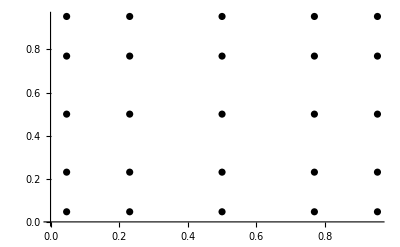

```mathematica
(*张量网格*)
REvaluate["{
standnw <- createNIGrid(dim=dimension, type=\"GLe\", level=5)
rescale(standnw, domain = matrix(c(0,0,1,1), ncol=2))
}"];
standpoints = REvaluate["getNodes(standnw)"];
standweights = Flatten@REvaluate["getWeights(standnw)"];

fig1 = ListPlot[standpoints,PlotStyle->Black,FrameStyle->Black,
BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->{Black,14,FontFamily->"Times"}]
(*Export["D:\\OneDrive - Personal\\OneDrive\\Thesis\\Figs\\二维张量网格.pdf",fig1]*)
```

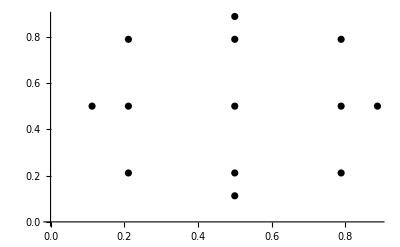

```mathematica
(*稀疏网格_level=3*)
REvaluate["{
sparenw <- createNIGrid(dim=dimension, type=\"GLe\", ndConstruction = \"sparse\",level=3)
rescale(sparenw, domain = matrix(c(0,0,1,1), ncol=2))
}"];

sparepoints = REvaluate["getNodes(sparenw)"][[1]];
spareweights = Flatten@REvaluate["getWeights(sparenw)"];

fig2 = ListPlot[sparepoints,PlotStyle->Black,FrameStyle->Black,
BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->{Black,14,FontFamily->"Times"}]

(*Export["D:\\OneDrive - Personal\\OneDrive\\Thesis\\Figs\\二维稀疏网格level2.pdf",fig2]*)
```

## 3. 交由MMA计算PDF

```mathematica
Dependentconvolution[copula_,t_?NumericQ,points_,weights_] := Module[{n,var,x,CopulaDerivative,quadrature},
(*用copula计算多维相关卷积，输入为1.用copula函数定义的联合分布; 2.所求的pdf的x值*)
(*该方法仍不适合维数过高的场景*)
n = Length@copula[[2]];
var = Array[x,n];
CopulaDerivative = PDF[copula,var]/.x[n]->t-Total[var[[1;;-2]]];
quadrature=Table[CopulaDerivative/.Table[x[j]->points[[i,j]],{j,1,n-1}],{i,1,Length[points]}].weights]
```

```mathematica
Dependentconvolution2[copula_,t_?NumericQ,points_,weights_] := Module[{n,var,x,newpoints,CopulaDerivative,quadrature},
(*第二种多重卷积形式,源自https://math.stackexchange.com/questions/3008915/multiple-convolution-closed-form*)
(*该方法对最后一维函数十分友好，可以用在高维场景中*)
n = Length@copula[[2]];
var = Array[x,n];
newpoints = points;
If[ n > 3 , newpoints[[All,2;;n-1]] = Table[points[[All,k]]-points[[All,k-1]],{k,2,n-1}]ᵀ];
CopulaDerivative = PDF[copula,var]/.{x[n]->t-var[[-2]]};
quadrature = Table[CopulaDerivative/.Table[x[j]->newpoints[[i,j]],{j,1,n-1}],{i,1,Length[points]}].weights]
```

```mathematica
MultipleDependentconvolution[copula_,t_?NumericQ] := Module[{n,var,x,CopulaDerivative},
(*用copula计算多维相关卷积，输入为1.用copula函数定义的联合分布; 2.所求的pdf的x值*)
(*该方法仍不适合维数过高的场景*)
	n = Length@copula[[2]];
	var = Array[x,n];
	CopulaDerivative = PDF[copula,var];
	NIntegrate[CopulaDerivative/.x[n]->t-Total[var[[1;;-2]]], ##]&@@Table[{x[i],-Infinity, Infinity},{i,1,n-1}]]
```

```mathematica
MultipleDependentconvolution2[copula_,t_?NumericQ] := Module[{n,var,x,CopulaDerivative},
(*第二种多重卷积形式,源自https://math.stackexchange.com/questions/3008915/multiple-convolution-closed-form*)
(*该方法对最后一维函数十分友好，可以用在高维场景中*)
	n = Length@copula[[2]];
	var = Array[x,n];
	CopulaDerivative = PDF[copula,var]/.{x[n]->t-var[[-2]]};
	If[ n > 2 , Table[CopulaDerivative/.x[k]->(x[k]-x[k-1]),{k,2,n-1}]];
	NIntegrate[CopulaDerivative, ##]&@@Table[{x[i],-Infinity, Infinity},{i,1,n-1}]]
```

```mathematica
MonteCarloconvolution[copula_,t_?NumericQ] := Module[{samples,accumulation},
(*用蒙特卡罗法计算多维相关卷积，输入为1.用copula函数定义的联合分布; 2.所求的pdf的x值*)
	samples = RandomVariate[copula,1000];
	accumulation = Total[samplesᵀ];
	PDF[HistogramDistribution[accumulation,100],t]]
```

```mathematica
NDDC[InputVariables_,DiscreteStep_]:=
Module[{VariableNumber,DCtimes,MaxMatrix,MinMatrix,PDFMatrix,NumberMatrix,ProbMatrix,NewInputVariables,COR,Copula,PALL,PM,Newxlablelength,BiaoyaoInputVariables,BiaoyaoNewInputVariables},
(*The method provided in [2]*)
(*离散化,计算离散概率*)
VariableNumber=Length[InputVariables];
DCtimes=VariableNumber-1;
MaxMatrix=Table[Max[InputVariables[[i]]],{i,1,VariableNumber}];
MinMatrix=Table[Min[InputVariables[[i]]],{i,1,VariableNumber}];
(*BiaoyaoInputVariables=Table[InputVariables[[i]]/MaxMatrix[[i]],{i,1,VariableNumber}];*)
PDFMatrix=Table[PDF[SmoothKernelDistribution[InputVariables[[i]]],x],{i,1,VariableNumber}];
NumberMatrix=Table[Ceiling[MaxMatrix[[i]]/DiscreteStep-0.5],{i,1,VariableNumber}];
ProbMatrix=Table[Table[Integrate[PDFMatrix[[i]],{x,(j-0.5)*DiscreteStep,(j+0.5)*DiscreteStep}],{j,1,NumberMatrix[[i]]}],{i,1,VariableNumber}];

(*计算累计相关性,构建copula*)
NewInputVariables=Table[∑_(j=1)^i InputVariables[[j]],{i,1,DCtimes}];(*第i次卷积所用的变量*)
(*BiaoyaoNewInputVariables=Table[∑_(j=1)^i BiaoyaoInputVariables[[j]],{i,1,DCtimes}];*)
COR=Table[Correlation[NewInputVariables[[i]],InputVariables[[i+1]]],{i,1,DCtimes}];
Copula=Table[CopulaDistribution[{"Binormal",COR[[i]]},Table[UniformDistribution[],{j,2}]],{i,1,DCtimes}];

(*卷积*)
PALL=Table[0,Total[NumberMatrix]];
PM=ProbMatrix[[1]];(*将第一次卷积变量初始化为P1*)
Newxlablelength=Table[∑_(j=1)^i NumberMatrix[[j]],{i,1,DCtimes}];(*求卷积之后新生成变量的长度*)
For[k=1,k≤DCtimes,k++,
For[i=1,i≤ (Newxlablelength[[k]]+NumberMatrix[[k+1]]),i++,
	For[j=1,j≤Newxlablelength[[k]],j++,
	If[0<i-j≤NumberMatrix[[k+1]],
	PALL[[i]]=PALL[[i]]+PDF[Copula[[k]],{Sum[PM[[m]],{m,j}],Sum[ProbMatrix[[k+1,n]],{n,i-j}]}]*PM[[j]]*ProbMatrix[[k+1,i-j]]];
	];
];
PM=PALL[[2;;]];
(*PM[[1]]=0.05;*)
PALL=Table[0,Total[NumberMatrix]];
];
PM]
```

```mathematica
rebuildPMF[xlable_,Prob_] := Piecewise[Append[Table[{Prob[[i]],xlable[[i]]≤ # <xlable[[i+1]]},{i,1,Length[Prob]}],{0,True}]]&;
```

```mathematica
Σ = Covariance[pvdata];(*总的协方差矩阵*)
histAccumulatePV[i_] := Module[{},cov = Σ[[1;;i,1;;i]]; CopulaDistribution[{"Multinormal",cov},edistHis[[1;;i]]]]
kdeAccumulatePV[i_] := Module[{},cov = Σ[[1;;i,1;;i]]; CopulaDistribution[{"Multinormal",cov},edistKDE[[1;;i]]]]
HistPV = histAccumulatePV[2];
kdePV = kdeAccumulatePV[2];
ansandtime = Timing[MultipleDependentconvolution[kdePV,2]];
Print["当t=2时，精确计算结果为",ansandtime[[2]]]
Print["Mathematica计算用时：",ansandtime[[1]],"s"]
```

当t=2时，精确计算结果为0.349483

Mathematica计算用时：6.78125s

#### PV1+PV2

```mathematica
kdePV = kdeAccumulatePV[2];
HistPV = histAccumulatePV[2];
Table[Max[pvdata[[All,i]]],{i,1,10}]
```

{0.933498,1.7953,1.9132,2.112,2.1895,2.81,3.3227,3.4458,3.866,5.0869}

```mathematica
(*张量高斯积分——准确解*)
precision = 12;
RSet["n",precision]; (*send all data to R*)
REvaluate["{
  nw.p <- createNIGrid(dim=1, type=\"GLe\", level=n)
  rescale(nw.p, domain = matrix(c(0, 0.9), ncol=2))
}"];
ProductRulePoints = REvaluate["getNodes(nw.p)"];
ProductRuleWeights = Flatten[REvaluate["getWeights(nw.p)"]];
Print[Dimensions[ProductRulePoints][[2]],"维张量高斯积分；","代数精度：",2*(precision-1)+1, "; 积分节点数=",Dimensions[ProductRulePoints][[1]]]
t = 2;
test = Timing[Dependentconvolution[kdePV,t,ProductRulePoints,ProductRuleWeights]];
Print["当t= ",t,"时,pdf为：",test[[2]]]
Print["单个积分计算用时：",test[[1]]]
```

1维张量高斯积分；代数精度：23; 积分节点数=12

当t= 2时,pdf为：0.350921

单个积分计算用时：0.015625

```mathematica
Dependentconvolution2[kdePV,t,ProductRulePoints,ProductRuleWeights] (*另一种积分方式计算*)
MultipleDependentconvolution[kdePV,t]
```

0.360567

0.349483

```mathematica
(*稀疏Gauss-Legendre积分*)
REvaluate["{
  nw.s <- createNIGrid(dim=1, type=\"GLe\", level=15, ndConstruction = \"sparse\")
  rescale(nw.s, domain = matrix(c(0, 0.9), ncol=2))
}"];
SparseRulePoints = REvaluate["getNodes(nw.s)"];
SparseRuleWeights = Flatten[REvaluate["getWeights(nw.s)"]];
Print[Dimensions[SparseRulePoints][[2]],"维稀疏Gauss-Legendre积分；","代数精度：",2*(precision-1)+1,";  积分节点数=",Dimensions[SparseRulePoints][[1]]]
t = 2;
test = Timing[Dependentconvolution[kdePV,t,SparseRulePoints,SparseRuleWeights]];
Print["当t= ",t,"时,pdf为：",test[[2]]]
Print["单个积分计算用时：",test[[1]]]
```

1维稀疏Gauss-Legendre积分；代数精度：23;  积分节点数=15

当t= 2时,pdf为：0.350077

单个积分计算用时：0.015625

```mathematica
a1 = Plot[MultipleDependentconvolution[kdePV,t],{t,-0.5,3},PlotStyle->Black,Filling->Axis,WorkingPrecision->MachinePrecision,
BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->{Black,14,FontFamily->"Times"},PlotPoints -> 100];
b1 = Histogram[Total[pvdata[[All,1;;2]]ᵀ],50,"PDF",AxesLabel->Automatic,AxesLabel->Automatic,FrameStyle->Black,BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->{Black,14,FontFamily->"Times"}];
```

$Aborted

```mathematica
samples = RandomVariate[kdePV,10000];
accumulation = Total[samplesᵀ];
h1 = Histogram[accumulation,50,"PDF",AxesLabel->Automatic,AxesLabel->Automatic,FrameStyle->Black,BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->{Black,14,FontFamily->"Times"}];
```

```mathematica
fig2 = Show[h1,a1,Frame->{{True,False},{True,False}},FrameLabel->{"PV output(MW)", "PDF"},Filling->Axis,
BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->{Black,14,FontFamily->"Times"}]
```

```mathematica
(*再试一下乘法*)
pdf1 = Table[PDF[edistKDE[[1]],x],{x,Flatten@ProductRulePoints}];
pdf2 = Table[PDF[edistKDE[[2]],x],{x,t-Flatten@ProductRulePoints}];

cdf1 = Table[CDF[edistKDE[[1]],x],{x,Flatten@ProductRulePoints}];
cdf2 = Table[CDF[edistKDE[[2]],x],{x,t-Flatten@ProductRulePoints}];

cov = Σ[[1;;2,1;;2]]; 
copulakernel = CopulaDistribution[{"Multinormal",cov}, {UniformDistribution[], UniformDistribution[]}];
copulapdf = Table[PDF[copulakernel,x],{x,{cdf1,cdf2}ᵀ}];

Total[copulapdf*pdf1*pdf2*ProductRuleWeights] (*完全一致*)
```

0.350921

```mathematica
(*蒙特卡洛计算得到的PDF曲线*)
samples = RandomVariate[kdePV,10000];
accumulation = Total[samplesᵀ];
Histogram[accumulation,50,"PDF",AxesLabel->Automatic,AxesLabel->Automatic,FrameStyle->Black,BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->{Black,14,FontFamily->"Times"}]
```

### 3维PV1+PV2+PV3

```mathematica
kdePV = kdeAccumulatePV[3];
HistPV = histAccumulatePV[3];
```

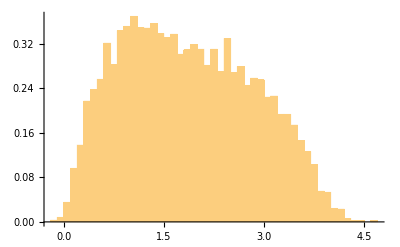

```mathematica
(*蒙特卡洛计算得到的PDF曲线*)
samples = RandomVariate[kdePV,10000];
accumulation = Total[samplesᵀ];
Histogram[accumulation,50,"PDF",AxesLabel->Automatic,AxesLabel->Automatic,FrameStyle->Black,BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->{Black,14,FontFamily->"Times"}]
```

```mathematica
(*张量高斯积分*)
precision = 12;
RSet["n",precision]; (*send all data to R*)
REvaluate["{nw.p <- createNIGrid(dim=2, type=\"GLe\", level=n);
           rescale(nw.p, domain = matrix(c(0,0,0.9,1.7), ncol=2))}"];
ProductRulePoints = REvaluate["getNodes(nw.p)"];
ProductRuleWeights = Flatten[REvaluate["getWeights(nw.p)"]];
```

```mathematica
t=2;
n = Length@kdePV[[2]];
var = Array[x,n];
newpoints = ProductRulePoints;
If[ n > 3 , newpoints[[All,2;;n-1]] = Table[ProductRulePoints[[All,k]]-ProductRulePoints[[All,k-1]],{k,2,n-1}]ᵀ]; (*3维就会出现Infinity的情况，需要改进*)
CopulaDerivative = PDF[kdePV,var]/.{x[n]->t-var[[-2]]};newpoints;
quadrature = Table[CopulaDerivative/.Table[x[j]->newpoints[[i,j]],{j,1,n-1}],{i,1,Length[newpoints]}].ProductRuleWeights
```

0.346464

### 4维PV1+PV2+PV3+PV4

```mathematica
HistPV = histAccumulatePV[4];
kdePV = kdeAccumulatePV[4];
```

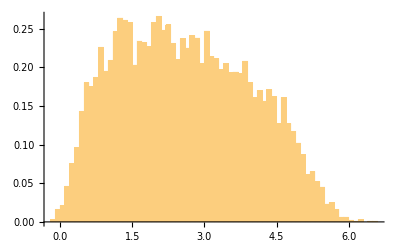

```mathematica
(*蒙特卡洛计算得到的PDF曲线*)
samples = RandomVariate[kdePV,10000];
accumulation = Total[samplesᵀ];
Histogram[accumulation,50,"PDF",AxesLabel->Automatic,AxesLabel->Automatic,FrameStyle->Black,BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->{Black,14,FontFamily->"Times"}]
```

```mathematica
(*张量高斯积分*)
precision = 12;
RSet["n",precision]; (*send all data to R*)
REvaluate["{nw.p <- createNIGrid(dim=3, type=\"GLe\", level=n);
           rescale(nw.p, domain = matrix(c(0,0,0,0.9,1.7,1.9), ncol=2))}"];
ProductRulePoints = REvaluate["getNodes(nw.p)"];
ProductRuleWeights = Flatten[REvaluate["getWeights(nw.p)"]];
Print[Dimensions[ProductRulePoints][[2]],"维张量Gauss-Legendre积分；","代数精度：",2*(precision-1)+1,";  积分节点数=",Dimensions[ProductRuleWeights][[1]]]
```

3维张量Gauss-Legendre积分；代数精度：23;  积分节点数=1728

```mathematica
t=5;
n = Length@kdePV[[2]];
var = Array[x,n];
CopulaDerivative = PDF[kdePV,var]/.x[n]->t-Total[var[[1;;-2]]];
quadrature=Table[CopulaDerivative/.Table[x[j]->ProductRulePoints[[i,j]],{j,1,n-1}],{i,1,Length[ProductRulePoints]}].ProductRuleWeights
```

0.119521

```mathematica
(*张量高斯积分*)
precision = 3;
RSet["n",precision]; (*send all data to R*)
REvaluate["{nw.s <- createNIGrid(dim=3, type=\"GLe\", level=n, ndConstruction = \"sparse\");
           rescale(nw.s, domain = matrix(c(0,0,0,0.9,1.7,1.9), ncol=2))}"];
SparseRulePoints = REvaluate["getNodes(nw.s)"][[1]];
SparseRuleWeights = Flatten[REvaluate["getWeights(nw.s)"]];
Print[Dimensions[SparseRulePoints][[2]],"维稀疏Gauss-Legendre积分；","代数精度：",2*(precision-1)+1,";  积分节点数=",Dimensions[SparseRulePoints][[1]]]
```

3维稀疏Gauss-Legendre积分；代数精度：5;  积分节点数=25

```mathematica
n = Length@kdePV[[2]];
var = Array[x,n];
CopulaDerivative = PDF[kdePV,var]/.x[n]->t-Total[var[[1;;-2]]];
quadrature=Table[CopulaDerivative/.Table[x[j]->SparseRulePoints[[i,j]],{j,1,n-1}],{i,1,Length[SparseRulePoints]}].SparseRuleWeights
```

1.31616

### 用乘法和Vinecopula计算10维PV出力之和

最后一个问题，各维的积分上下限各是多少？
原则上积分上下限应该是选取各维的最大值和最小值。但直接取最大最小值再积分会导致计算copula时出现copulaPDF为无穷的情况，此时无法求解，应该在允许的条件下一定程度上放缩积分区间范围。
积分的区间和维数确实是本方法的一个关键，为了便于积分，可以考虑将维数从小到大排列一下，让积分区间最大的放到最后

```mathematica
HistPV = histAccumulatePV[10];
kdePV = kdeAccumulatePV[10];
Table[Max[pvdata[[All,i]]],{i,1,10}]
```

{0.933498,1.7953,1.9132,2.112,2.1895,2.81,3.3227,3.4458,3.866,5.0869}

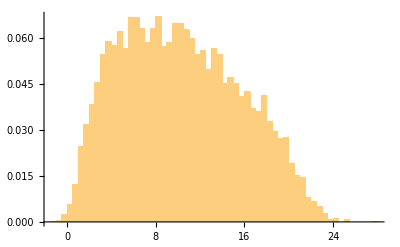
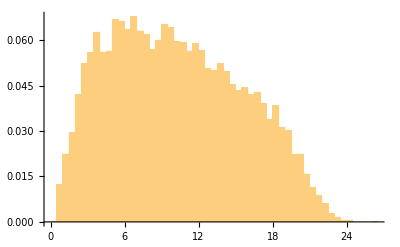

```mathematica
(*蒙特卡洛计算得到的PDF曲线*)
samples = RandomVariate[kdePV,10000];samples2 = RandomVariate[HistPV,10000];
accumulation = Total[samplesᵀ];accumulation2 = Total[samples2ᵀ];
h2 = Histogram[accumulation,50,"PDF",AxesLabel->Automatic,AxesLabel->Automatic,FrameStyle->Black,BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->{Black,14,FontFamily->"Times"}];
h3 = Histogram[accumulation2,50,"PDF",AxesLabel->Automatic,AxesLabel->Automatic,FrameStyle->Black,BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->{Black,14,FontFamily->"Times"}];
List[h2,h3]
```

```mathematica
hist10 = HistogramDistribution[accumulation2];
```

```mathematica
(*张量高斯积分*)
precision = 4;
RSet["n",precision]; (*send all data to R*)
REvaluate["{nw.p <- createNIGrid(dim=9, type=\"GLe\", level=n);
           rescale(nw.p, domain = matrix(c(0,0,0,0,0,0,0,0,0,0.9,1.7,1.9,2,2.1,2.8,3.3,3.4,3.8), ncol=2))}"];
ProductRulePoints = REvaluate["getNodes(nw.p)"];
ProductRuleWeights = Flatten[REvaluate["getWeights(nw.p)"]];
Print[Dimensions[ProductRulePoints][[2]],"维Gauss-Legendre积分；","代数精度：",2*(precision-1)+1,";  积分节点数=",Dimensions[ProductRulePoints][[1]]]
```

9维Gauss-Legendre积分；代数精度：7;  积分节点数=262144

```mathematica
(*将基于vine copula的高维卷积包装为函数*)
plotAccumulatePVproduct[t_?NumericQ,pdffront_,cdffront_] := Module[{pdf,cdf,vinepdf,pdfend,cdfend},
pdfend = Table[PDF[edistKDE[[10]],t-Total[ProductRulePoints[[i]]]],{i,1,Length[ProductRuleWeights]}];
cdfend = Table[CDF[edistKDE[[10]],t-Total[ProductRulePoints[[i]]]],{i,1,Length[ProductRuleWeights]}];

pdf = Append[pdffrontᵀ,pdfend]ᵀ;
cdf = Append[cdffrontᵀ,cdfend]ᵀ;
RSet["cdf",cdf]; (*将边缘cdf值赋给R*)
REvaluate["{copulaPDF <- RVinePDF(cdf, VineCoplaModel);}"];
vinepdf = REvaluate["copulaPDF"];
Total[vinepdf*Product[pdf[[All,i]],{i,1,10}]*ProductRuleWeights]];
```

```mathematica
(*
ProductRulePoints = REvaluate["load(\"D:/OneDrive - Personal/OneDrive/Coding History/R/Convulation_nodes.RData\")"];
ProductRuleWeights = REvaluate["weight"];
ProductRulePoints = Import["D:/OneDrive - Personal/OneDrive/Coding History/R/nodesData.csv"];
*)
pdffrontProduct = Table[Table[PDF[edistKDE[[i]],ProductRulePoints[[j,i]]],{i,1,9}],{j,1,Length[ProductRuleWeights]}];
cdffrontProduct = Table[Table[CDF[edistKDE[[i]],ProductRulePoints[[j,i]]],{i,1,9}],{j,1,Length[ProductRuleWeights]}];
```

```mathematica
plotAccumulatePVproduct[6,pdffrontProduct,cdffrontProduct]//Timing
```

{39.2813,0.213358}

```mathematica
(*稀疏高斯积分*)
precision = 6;
RSet["n",precision]; (*send all data to R*)
REvaluate["{nw.s <- createNIGrid(dim=9, type=\"GLe\", level=n, ndConstruction = \"sparse\");
           rescale(nw.s, domain = matrix(c(0,0,0,0,0,0,0,0,0,2.6,5,1.5,2,3,3,1.5,1.6,3), ncol=2))}"];
SparseRulePoints = REvaluate["getNodes(nw.s)"][[1]];
SparseRuleWeights = Flatten[REvaluate["getWeights(nw.s)"]];
Print[Dimensions[SparseRulePoints][[2]],"维稀疏Gauss-Legendre积分；","代数精度：",2*(precision-1)+1,";  积分节点数=",Dimensions[SparseRulePoints][[1]]]
```

9维稀疏Gauss-Legendre积分；代数精度：11;  积分节点数=25315

```mathematica
(*将基于vine copula的高维卷积包装为函数*)
plotAccumulatePVsparse[t_?NumericQ,pdffront_,cdffront_] := Module[{pdf,cdf,vinepdf,pdfend,cdfend},
pdfend = Table[PDF[edistKDE[[10]],t-Total[SparseRulePoints[[i]]]],{i,1,Length[SparseRuleWeights]}];
cdfend = Table[CDF[edistKDE[[10]],t-Total[SparseRulePoints[[i]]]],{i,1,Length[SparseRuleWeights]}];

pdf = Append[pdffrontᵀ,pdfend]ᵀ;
cdf = Append[cdffrontᵀ,cdfend]ᵀ;
RSet["cdf",cdf]; (*将边缘cdf值赋给R*)
REvaluate["{copulaPDF <- RVinePDF(cdf, VineCoplaModel);}"];
vinepdf = REvaluate["copulaPDF"];
Total[vinepdf*Product[pdf[[All,i]],{i,1,10}]*SparseRuleWeights]];
```

```mathematica
pdffrontSparse = Table[Table[PDF[edistKDE[[i]],SparseRulePoints[[j,i]]],{i,1,9}],{j,1,Length[SparseRuleWeights]}];
cdffrontSparse = Table[Table[CDF[edistKDE[[i]],SparseRulePoints[[j,i]]],{i,1,9}],{j,1,Length[SparseRuleWeights]}];
```

```mathematica
plotAccumulatePVsparse[6,pdffrontSparse,cdffrontSparse]//Timing
```

{0.875,0.}

```mathematica
(*将基于Gaussian copula的高维卷积包装为函数*)
plotGaussianPV[t_?NumericQ] := Module[{pdffront,cdffront,pdf,cdf,vinepdf,pdfend,cdfend},
pdffront = Table[Table[PDF[edistGMM[[i]],ProductRulePoints[[j,i]]],{i,1,9}],{j,1,Length[ProductRuleWeights]}];
cdffront = Table[Table[CDF[edistGMM[[i]],ProductRulePoints[[j,i]]],{i,1,9}],{j,1,Length[ProductRuleWeights]}];
pdfend = Table[PDF[edistGMM[[10]],t-Total[ProductRulePoints[[i]]]],{i,1,Length[ProductRuleWeights]}];
cdfend = Table[CDF[edistGMM[[10]],t-Total[ProductRulePoints[[i]]]],{i,1,Length[ProductRuleWeights]}];

pdf = Append[pdffrontᵀ,pdfend]ᵀ;
cdf = Append[cdffrontᵀ,cdfend]ᵀ;
cov = Σ[[1;;10,1;;10]]; 
copulakernel = CopulaDistribution[{"Multinormal",cov}, Table[UniformDistribution[],10]];
copulapdf = Table[PDF[MultinormalDistribution[cov],cdf[[i]]],{i,1,Length[ProductRuleWeights]}]; (*用Gaussian Copula计算得到的结果*)
Total[copulapdf*Product[pdf[[All,i]],{i,1,10}]*ProductRuleWeights]];
```

```mathematica
(*将基于vine copula的高维卷积包装为函数*)
plotAccumulatePV[t_?NumericQ] := Module[{pdf,cdf,vinepdf,pdffront,cdffront,pdfmid,cdfmid,pdfend,cdfend},
pdffront = PDF[edistKDE[[1]],SparseRulePoints[[All,1]]];
cdffront = CDF[edistKDE[[1]],SparseRulePoints[[All,1]]];
pdfmid = Table[PDF[edistKDE[[i]],SparseRulePoints[[All,i]]-SparseRulePoints[[All,i-1]]],{i,2,9}];
cdfmid = Table[CDF[edistKDE[[i]],SparseRulePoints[[All,i]]-SparseRulePoints[[All,i-1]]],{i,2,9}];
pdfend = PDF[edistKDE[[10]],t-SparseRulePoints[[All,9]]];
cdfend = CDF[edistKDE[[10]],t-SparseRulePoints[[All,9]]];

pdf = Prepend[Append[pdfmid,pdfend],pdffront]ᵀ;
cdf = Prepend[Append[cdfmid,cdfend],cdffront]ᵀ;
pdf = pdf/.x_/;x<=0 ->0.01;
cdf = cdf/.x_/;x<=0 ->0.01;
RSet["cdf",cdf]; (*将边缘cdf值赋给R*)
REvaluate["{copulaPDF <- RVinePDF(cdf, VineCoplaModel);}"];
vinepdf = REvaluate["copulaPDF"];
Total[vinepdf*Product[pdf[[All,i]],{i,1,10}]*SparseRuleWeights]];
```

```mathematica
Print["实际光伏出力之和的均值为：",Mean[Total[pvdataᵀ]]," MW"]
Print["实际光伏出力之和的最大值为：",Max[Total[pvdataᵀ]]," MW"]
```

实际光伏出力之和的均值为：23.7039 MW

实际光伏出力之和的最大值为：51.6787 MW

```mathematica
(*DDC method*)
PV9={TransPVdata[[1]],TransPVdata[[2]],TransPVdata[[3]],TransPVdata[[4]],TransPVdata[[5]],TransPVdata[[6]],TransPVdata[[7]],TransPVdata[[8]],TransPVdata[[9]],TransPVdata[[10]]};
```

```mathematica
timeAndResultofDDC = Timing[NDDC[PV9,0.04]]
DC9 = timeAndResultofDDC[[2]]*25
```

```mathematica
xlable1=Table[0.04*i,{i,1,2000}];
b9=Plot[{rebuildPMF[xlable1,DC9][x]},{x,0,25},PlotStyle->{Orange,Dashed},PlotLegends->{"DDC"},LabelStyle->{Black,14,FontFamily->"Times"}];
```

```mathematica
(*利用VineCopula计算*)
Timing[REvaluate["{copulaSample <- RVineSim(1000000,VineCoplaModel);}"];
vineCopSample = REvaluate["copulaSample"][[1]];
vineSamples = Table[Quantile[edistHis[[i]],vineCopSample[[All,i]]],{i,1,10}];
vinesampleSum = Total[vineSamples];
PDF[HistogramDistribution[vinesampleSum],10]]
```

{779.734,0.0566315}

```mathematica
vinedist = SmoothKernelDistribution[vinesampleSum];
v9 = Plot[PDF[vinedist,x],{x,0,25},PlotStyle->{Red,Thick},PlotLegends->{"MDC"},LabelStyle->{Black,14,FontFamily->"Times"}];
```

```mathematica
hAll = Histogram[vinesampleSum,50,"PDF",ChartStyle->LightBlue, AxesLabel->Automatic,AxesLabel->Automatic,ChartLegends->{"MC"},
       FrameStyle->Black,BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->{Black,14,FontFamily->"Times"}];
```

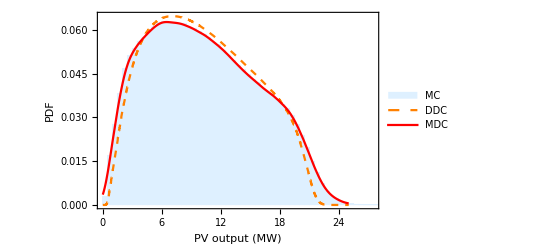

```mathematica
fig9=Show[hAll,b9,v9,Frame->{{True,False},{True,False}},FrameLabel->{"PV output (MW)", "PDF"},
BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->{Black,14,FontFamily->"Times"}]
```

```mathematica
Export["D:\\OneDrive - Personal\\OneDrive\\Papers\\07The price of uncertainty\\Figs\\PV_PDF.pdf",fig9]
```

D:\OneDrive - Personal\OneDrive\Papers\07The price of uncertainty\Figs\PV_PDF.pdf